### dopplerD_partial_derivatives.nb Partial derivatives of Doppler equation Evaluate dopplerC_estimate.nb first. Carl Tape and Bella Seppi October 20, 2025

```mathematica
ClearParms
```

### Partial derivatives

```mathematica
Clear[partialv,partialfs,partialt0,partiald0,partialc]
Clear[partialvX,partialfsX,partialt0X,partiald0X,partialcX]
```

```mathematica
Clear[vv,t0s,d0s,fss,cc]
partialv[v_,t0_,d0_,fs_,c_,tp_]:=D[Ft[vv,t0,d0,fs,c,tp],vv]/. vv->v
partialfs[v_,t0_,d0_,fs_,c_,tp_]:=D[Ft[v,t0,d0,fss,c,tp],fss]/. fss->fs
partialt0[v_,t0_,d0_,fs_,c_,tp_]:=D[Ft[v,t0s,d0,fs,c,tp],t0s]/. t0s->t0
partiald0[v_,t0_,d0_,fs_,c_,tp_]:=D[Ft[v,t0,d0s,fs,c,tp],d0s]/. d0s->d0
partialc[v_,t0_,d0_,fs_,c_,tp_]:=D[Ft[v,t0,d0,fs,cc,tp],cc]/. cc->c
```

### This factor will help shorten the explicit expressions

```mathematica
G[v_,t0_,d0_,c_,tp_]:=√(1-v^2/c^2+((t0-tp)^2 v^2)/d0^2)
```

### Partial derivative expressions, fully simplified. They can be commented out, since we define explicit expressions.

### Speed of source, v

```mathematica
(*FullSimplify[D[Ft[v,t0,d0,fs,c,tp],v]]*)
```

```mathematica
partialvX[v_,t0_,d0_,fs_,c_,tp_]:=(fs v (2 d0^4 v^4-d0^2 (t0-tp)^2 v^6+3 c d0^3 (-t0+tp) v^4 G[v,t0,d0,c,tp]+c^5 d0 (t0-tp) (2 d0^2+(t0-tp)^2 v^2) G[v,t0,d0,c,tp]+c^3 d0 (t0-tp) v^2 (d0^2+3 (t0-tp)^2 v^2) G[v,t0,d0,c,tp]+c^2 v^2 (-4 d0^4-5 d0^2 (t0-tp)^2 v^2+(t0-tp)^4 v^4)+c^4 (2 d0^4+6 d0^2 (t0-tp)^2 v^2+3 (t0-tp)^4 v^4)))/(d0 (c-v) (c+v) G[v,t0,d0,c,tp] √(d0^2+(c^2 v^2 (c t0-c tp+d0 G[v,t0,d0,c,tp])^2)/((c^2-v^2)^2)) (c (t0-tp) v^2+d0 v^2 G[v,t0,d0,c,tp]-c^2 √(d0^2+(c^2 v^2 (c t0-c tp+d0 G[v,t0,d0,c,tp])^2)/((c^2-v^2)^2))+v^2 √(d0^2+(c^2 v^2 (c t0-c tp+d0 G[v,t0,d0,c,tp])^2)/((c^2-v^2)^2)))^2)
```

### Unshifted frequency, fs (note: it does not depend on fs)

```mathematica
(*FullSimplify[D[Ft[v,t0,d0,fs,c,tp],fs]]*)
```

```mathematica
partialfsX[v_,t0_,d0_,fs_,c_,tp_]:=(1-(v^2 (c t0-c tp+d0 G[v,t0,d0,c,tp]))/((c^2-v^2) √(d0^2+(c^2 v^2 (c t0-c tp+d0 G[v,t0,d0,c,tp])^2)/((c^2-v^2)^2))))^-1
```

### Arrival time, t0

```mathematica
(*FullSimplify[D[Ft[v,t0,d0,fs,c,tp],t0]]*)
```

```mathematica
partialt0X[v_,t0_,d0_,fs_,c_,tp_]:=(d0 fs (c-v) v^2 (c+v) ((t0-tp) v^2+c d0 G[v,t0,d0,c,tp]))/(G[v,t0,d0,c,tp] √(d0^2+(c^2 v^2 (c t0-c tp+d0 G[v,t0,d0,c,tp])^2)/((c^2-v^2)^2)) (c (t0-tp) v^2+d0 v^2 G[v,t0,d0,c,tp]-c^2 √(d0^2+(c^2 v^2 (c t0-c tp+d0 G[v,t0,d0,c,tp])^2)/((c^2-v^2)^2))+v^2 √(d0^2+(c^2 v^2 (c t0-c tp+d0 G[v,t0,d0,c,tp])^2)/((c^2-v^2)^2)))^2)
```

### Distance to object, d0

```mathematica
(*FullSimplify[D[Ft[v,t0,d0,fs,c,tp],d0]]*)
```

```mathematica
partiald0X[v_,t0_,d0_,fs_,c_,tp_]:=(fs (t0-tp) v^2 (-c^2+v^2) ((t0-tp) v^2+c d0 G[v,t0,d0,c,tp]))/(G[v,t0,d0,c,tp] √(d0^2+(c^2 v^2 (c t0-c tp+d0 G[v,t0,d0,c,tp])^2)/((c^2-v^2)^2)) (c (t0-tp) v^2+d0 v^2 √(1-v^2/c^2+((t0-tp)^2 v^2)/d0^2)-c^2 √(d0^2+(c^2 v^2 (c t0-c tp+d0 G[v,t0,d0,c,tp])^2)/((c^2-v^2)^2))+v^2 √(d0^2+(c^2 v^2 (c t0-c tp+d0 G[v,t0,d0,c,tp])^2)/((c^2-v^2)^2)))^2)
```

### Acoustic wavespeed, c

```mathematica
(*FullSimplify[D[Ft[v,t0,d0,fs,c,tp],c]]*)
```

```mathematica
partialcX[v_,t0_,d0_,fs_,c_,tp_]:=-((fs v^2 (2 d0^4 v^4-2 d0^2 (t0-tp)^2 v^6+4 c d0^3 (-t0+tp) v^4 G[v,t0,d0,c,tp]+c^5 d0 (t0-tp) (d0^2+(t0-tp)^2 v^2) G[v,t0,d0,c,tp]+3 c^3 d0 (t0-tp) v^2 (d0^2+(t0-tp)^2 v^2) G[v,t0,d0,c,tp]+c^2 v^2 (-4 d0^4-3 d0^2 (t0-tp)^2 v^2+(t0-tp)^4 v^4)+c^4 (2 d0^4+5 d0^2 (t0-tp)^2 v^2+3 (t0-tp)^4 v^4)))/(c d0 (c-v) (c+v) G[v,t0,d0,c,tp] √(d0^2+(c^2 v^2  (c t0-c tp+d0 G[v,t0,d0,c,tp])^2)/((c^2-v^2)^2)) (c (t0-tp) v^2+d0 v^2 G[v,t0,d0,c,tp]-c^2 √(d0^2+(c^2 v^2 (c t0-c tp+d0 G[v,t0,d0,c,tp])^2)/((c^2-v^2)^2))+v^2 √(d0^2+(c^2 v^2 (c t0-c tp+d0 G[v,t0,d0,c,tp])^2)/((c^2-v^2)^2)))^2))
```

## Unused

### Find the maximal slope of the Doppler curve. That means finding the root for the second derivative.

```mathematica
(* Solve[D[Ft[v,t0,d0,fs,c,tp],{tp,2}]==0,tp] *)  (* not sure if this will run *)
```

### Find the inflection points by setting the third derivative to zero and solving.

```mathematica
(* Solve[D[Ft[v,t0,d0,fs,c,tp],{tp,3}]==0,tp] *)  (* this probably does not finish *)
```

## Example values for a Doppler curve

```mathematica
SetParms
```

```mathematica
thwid =100;
```

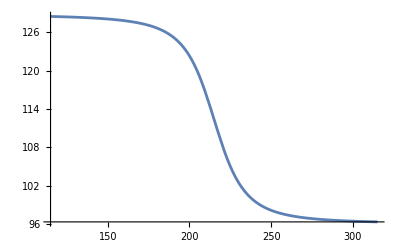

```mathematica
Plot[Ft[v,t0,d0,fs,c,tp],{tp,t0-thwid,t0+thwid}]
```

## Partial derivatives for v, t0, d0, fs, c, each plotted as a function of tp

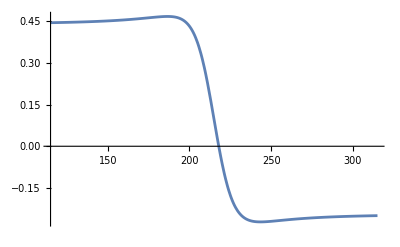

```mathematica
Plot[partialv[v,t0,d0,fs,c,tp],{tp,t0-thwid,t0+thwid}]
```

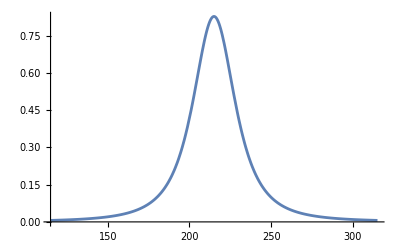

```mathematica
Plot[partialt0[v,t0,d0,fs,c,tp],{tp,t0-thwid,t0+thwid}]
```

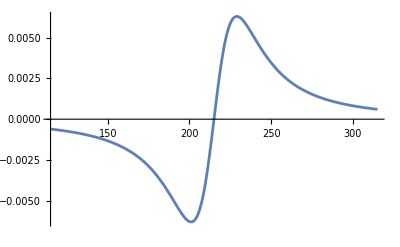

```mathematica
Plot[partiald0[v,t0,d0,fs,c,tp],{tp,t0-thwid,t0+thwid}]
```

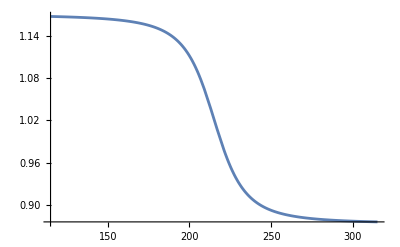

```mathematica
Plot[partialfs[v,t0,d0,fs,c,tp],{tp,t0-thwid,t0+thwid}]
```

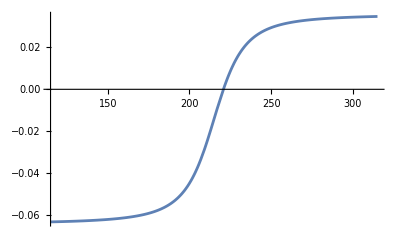

```mathematica
Plot[partialc[v,t0,d0,fs,c,tp],{tp,t0-thwid,t0+thwid}]
```

## Test values (for checking Python)

### first check

```mathematica
Ft[v,t0,d0,fs,c,t0]
Ft[v,t0,d0,fs,c,tp0]
fs
```

112.388

110.

110.

### choose a (sensor) time point:

```mathematica
tp = 200.;
t[v,t0,d0,c,tp]
Ft[v,t0,d0,fs,c,tp]
```

-19.0237

122.286

### compare explicit expressions with expressions based on D[ ]:

```mathematica
partialv[v,t0,d0,fs,c,tp]
partialvX[v,t0,d0,fs,c,tp]
partialt0[v,t0,d0,fs,c,tp]
partialt0X[v,t0,d0,fs,c,tp]
partiald0[v,t0,d0,fs,c,tp]
partiald0X[v,t0,d0,fs,c,tp]
partialfs[v,t0,d0,fs,c,tp]
partialfsX[v,t0,d0,fs,c,tp]
partialc[v,t0,d0,fs,c,tp]
partialcX[v,t0,d0,fs,c,tp]
```

0.432579

0.432579

0.419014

0.419014

-0.00628521

-0.00628521

1.11169

1.11169

-0.044734

-0.044734